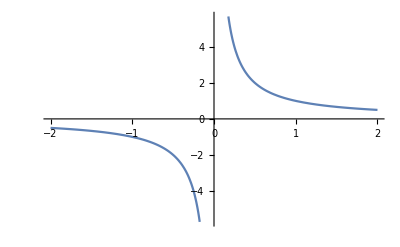

```mathematica
Plot[1/x, {x, -2,2}]
```

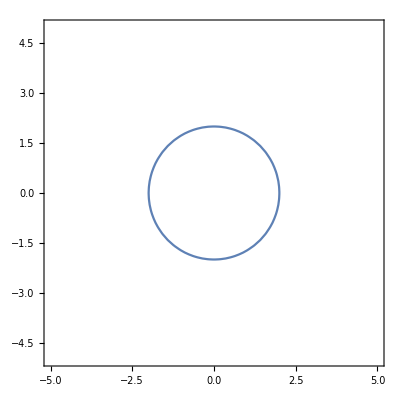

```mathematica
ContourPlot[x^2 + y^2 ==4, {x,-5,5}, {y,-5,5}]
```

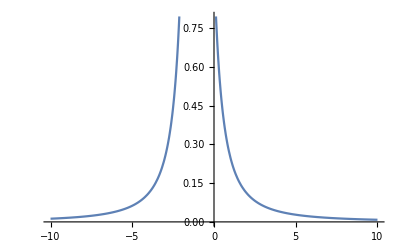

```mathematica
Plot[(1/(1+x))^2,{x,-10,10}]
```

```mathematica
f= Function[{x},Evaluate[Composition[(x-3)/(x+2),(3+2x)/(1-x)]]]
```

Function[{x},(-3+x)/(2+x)@*(3+2 x)/(1-x)]

```mathematica
f@2
```

(-1/4)@*(-7)

```mathematica
f = Composition[(x-3)/(x+2),(3+2x)/(1-x)]
```

(-3+x)/(2+x)@*(3+2 x)/(1-x)

```mathematica
f@x
```

(-3+x)/(2+x)[(3+2 x)/(1-x)[x]]

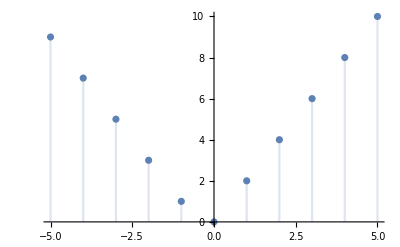

```mathematica
DiscretePlot[Piecewise[{{2*n,n≥0},{-2*n-1,n<0}}],{n,-5,5}]
```

```mathematica
Manipulate[Plot[Evaluate[Sum[(1/2)^n*Cos[3^n*Pi*x],{n,0,terms}]],{x,Clip[x0-Exp@zoom,{0,3}],Clip[x0+Exp@zoom,{0,3}]},PlotStyle->Table[Thickness[0.0085-0.002 k],{k,3}],GridLines->{{x0},{}}],{{terms,2},1,10,1},{{x0,1.5},0.4,2.6},{{zoom,Log[3.]},-6.,Log[3.]}]
```

```mathematica
Table[(n^2-n)/2,{n,1,20}]
```

{0,1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190}

```mathematica
f[n_]:=Sum[1,{i,1,n},{j,i+1,n},{k,i+j-1,n}]
f2[n_]=FindSequenceFunction[f/@Range[10],n]//FullSimplify
```

1/48 (3 (-1+(-1)^n)+2 n (2+n) (-1+2 n))

```mathematica
Solve[2^{-x}+4^{-x}+8^{-x}==1,x]//N
```

{{x→ConditionalExpression[0.879146+(0.+9.06472 ⅈ) C[1],C[1]∈ℤ]},{x→ConditionalExpression[(-0.439573+3.13964 ⅈ)+(0.+9.06472 ⅈ) C[1],C[1]∈ℤ]},{x→ConditionalExpression[(-0.439573-3.13964 ⅈ)+(0.+9.06472 ⅈ) C[1],C[1]∈ℤ]}}

```mathematica
Factor[x^3-5x^2+8x-4]
```